# Generating Nets for Random Convex Polyhedra

Sunny Wang

Jeremy Stratton-Smith, Chip Hurst

## Abstract

This project is essentially a visualization of Shephard’s conjecture, which states that every convex polyhedron admits a self-nonoverlapping unfolding. Currently, there exists unfolding data for several predefined polyhedra, and my goal is to create a function that do this for any random convex polyhedron. I chose this project because of my love for origami and interest in 3D modeling.

## Generating a graph for the faces of the polyhedron

My first step was to create a graph that captures the relationship between faces of the polyhedron so that it could be used later to generate the net. The built in function DualPolyhedron converts the polyhedron to one where each vertex corresponds to a face on the original. I then extracted the vertices of the dual polyhedron, and partitioned and sorted them, allowing me to create a graph using those vertices.

```mathematica
polyhedron = RandomPolyhedron[{"ConvexHull",25}]
```

Polyhedron[…]

```mathematica
ClearAll[polyhedronfacegraph];

polyhedronfacegraph[polyhedron_]:= 
Block[{dualpolyhedron, vertexlist, vertexpairings, sortedvertices},

	 dualpolyhedron = DualPolyhedron[polyhedron];  (* Generate the dual polyhedron *)
     vertexlist = dualpolyhedron[[2]];   
     
     vertexpairings = Flatten[Table[
     Append[
     Partition[vertexlist[[n]], 2, 1], (* Partitions into groups of two *)
     {Last[vertexlist[[n]]], First[vertexlist[[n]]]}],  (* Appends the case where the last should be connected to the first *)
     {n, 1, Length[vertexlist]}], 
     1];
     
     sortedvertices = Sort /@ vertexpairings // DeleteDuplicates; (* Deletes duplicates by sorting them first *)

Graph[UndirectedEdge@@@sortedvertices,VertexLabels -> "Name"] (* Graphs the sorted vertices and labels it *)
]
```

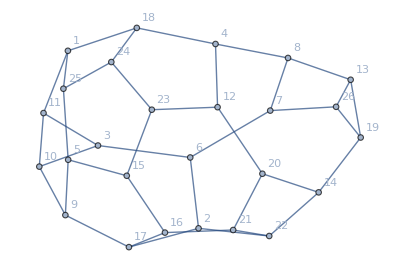

```mathematica
dualgraph = polyhedronfacegraph[polyhedron]
```

## Creating a function for generating all spanning trees

I then used the graph to generate different paths in which a polyhedron could unfold. One way to do this is by using a spanning tree, a tree generated from a graph that retains the same amount of vertices while having the minimum amount of edges. This essentially creates a simple version of what the final net should look like. Each vertex represents a face, and connections between them signify that they are adjacent. It is important to note that not every spanning tree will correspond to a non overlapping net, which is why I generate a spanning tree from every possible vertex.

Iterate through every vertex as a possible starting point.

```mathematica
ClearAll[generatetrees];

generatetrees[graph_] := Table[FindSpanningTree[{graph, n}], {n, 1, VertexCount[graph]}]
```

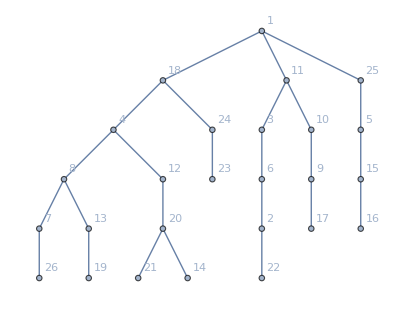
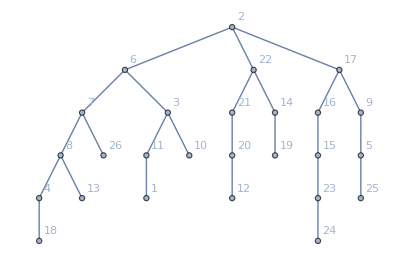
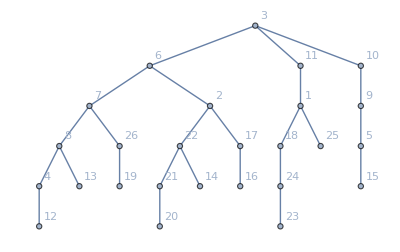
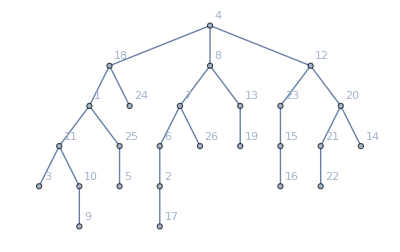
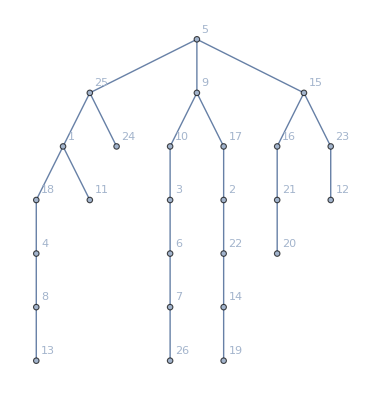
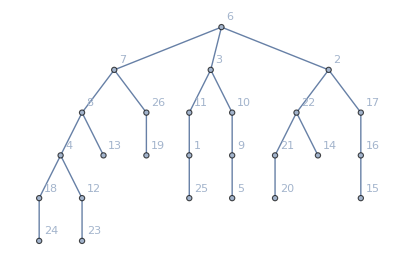
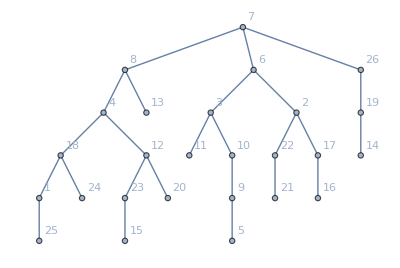

```mathematica
generatetrees[dualgraph][[1;;7]]
```

## Generating coordinates of the net of the polyhedron

To create the net of the polyhedron, I had to implement an unfolding algorithm. My first approach was to extract each face individually, but that ended up complicating the transformations. My final algorithm consisted of applying one transformation to move one face to the xy plane, then unfolding using the vertices on the spanning tree.

Create a function to get the normal vector to a plane.

```mathematica
ClearAll[normvector];

normvector[coords_] :=
Cross[coords[[2]] - coords[[1]], coords[[3]] - coords[[1]]];
```

Create a function to generate transformations according to the spanning tree, similar to physically unfolding an object.

```mathematica
ClearAll[unfold];

unfold[meshlist_, normals_, transformedrotation_][u_, v_, _] /; (u =!= v) :=

	Block[{edgecoord1, edgecoord2, angle, rotation},
		{edgecoord1, edgecoord2} = Intersection @@ meshlist⟦{u, v}⟧; 
		angle = DihedralAngle[{edgecoord1, edgecoord2}, normals⟦{u, v}⟧];
		rotation = RotationTransform[angle, edgecoord2 - edgecoord1, Mean[{edgecoord1, edgecoord2}]];
		transformedrotation[u] = transformedrotation[v]@*rotation;
		Sow[transformedrotation[u] @ meshlist⟦u⟧, "flat"];
	]
```

Transform the polyhedron so that one face is lying on the xy plane,  then apply unfold using the list of spanning trees.

```mathematica
ClearAll[generatenetcoords];

generatenetcoords[mesh_, tree_]:=
	Block[{transformations, transformedmesh, meshlist, transformedmeshlist, normals, polygonfaces, transformedrotation},
		polygonfaces = Reap[
		
		    meshlist = MeshPrimitives[mesh, 2][[All, 1]];
		    
			transformations =      (* Creates a transformation matrix *)
			RotationTransform[{normvector[meshlist[[1]]], {0, 0, -1}}] @*     (* rotates the normal vector of the face so that it is pointing down *)
			TranslationTransform[-PropertyValue[{mesh, {2, 1}}, MeshCellCentroid]];   (* translates the face *)
			
			transformedmesh = TransformedRegion[mesh, transformations];      (* Applies the transformation matrix *)
			
			transformedmeshlist = MeshPrimitives[transformedmesh, 2][[All, 1]];      (* Creates mesh primitives for the transformed mesh *)
			
			normals = normvector[#] &/@ transformedmeshlist;     (* Finds all the normal vectors for the faces *)

			Sow[transformedmeshlist[[1]], "flat"];
			
			transformedrotation[1] = TransformationFunction[IdentityMatrix[4]];
			
			BreadthFirstScan[tree, 1, "DiscoverVertex" -> unfold[transformedmeshlist, normals, transformedrotation]];,   (* Runs unfold on each discovered vertex *)
			 {"flat"}][[-1, All, 1]];
		Chop[polygonfaces]
	]
```

## Generating a list of all possible nets

All of the functions are put together in generateallnets. This function first defines local variables using the previous functions, then iterates through every spanning tree to produce a net using unfold. Each net is tested for overlap by calculating the surface area of the original polyhedron and comparing it to the surface area of the net. Only nets where the two surface areas are equal are appended to the list that is returned.

```mathematica
ClearAll[generateallnets];

generateallnets[polyhedron_] := 
Block[{netcoords, trees, graph, mesh, surfacearea, netsurfacearea, goodnets},

mesh = BoundaryDiscretizeGraphics[polyhedron];    (* Assign values using other functions *)
graph = polyhedronfacegraph[polyhedron];
trees = generatetrees[graph];

goodnets = {};   (* Start with an empty list of non overlapping nets *)

Table[     (* Iterate through every spanning tree in the list of trees *)

netcoords = First@generatenetcoords[mesh, trees[[treeposition]]];        (* generates coordinates for  *)
netcoords = Table[Delete[netcoords[[n, m]], {3}], {n, 1, Length[netcoords]}, {m, 1, 3}];        (* Delete the third element of each coordinate so it becomes two dimensional *)

surfacearea = SurfaceArea[polyhedron];
netsurfacearea = RegionMeasure[RegionUnion[Polygon /@ netcoords]];

If[surfacearea == netsurfacearea,             (* Check if the two surface areas are equal *)
AppendTo[goodnets, Graphics[{Hue[0.94, 0.22, 1.], EdgeForm[{Thin, Pink}], Polygon /@ netcoords}]]         (* Append it to the list *)
];,  

{treeposition, 1, Length[trees]}];    

Row[{Graphics3D[polyhedron], goodnets}]
]
```

## Outputs

Upon taking a polyhedron object in as its argument, generateallnets returns a 3D graphic of the original polyhedron and a list of all possible nets.

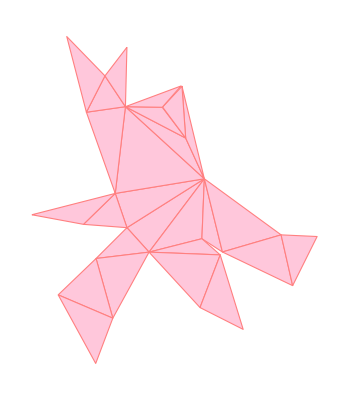
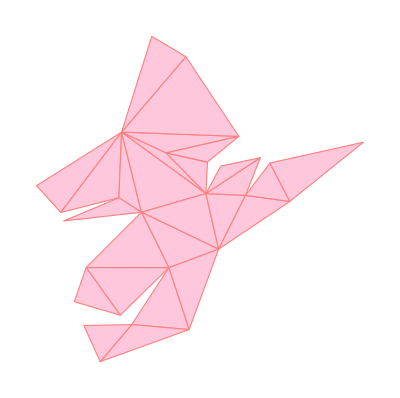
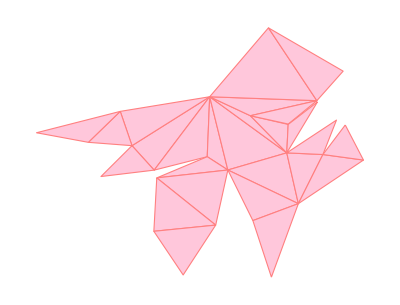
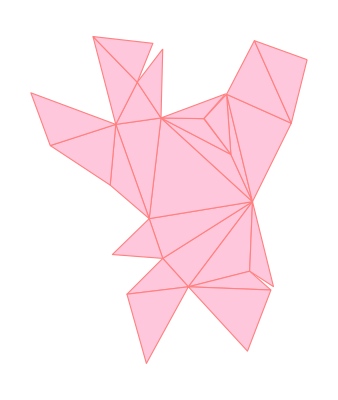
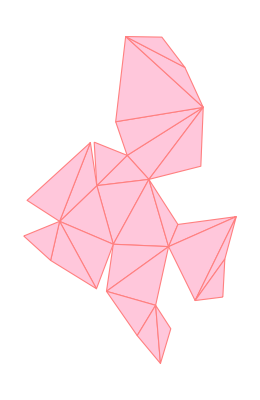
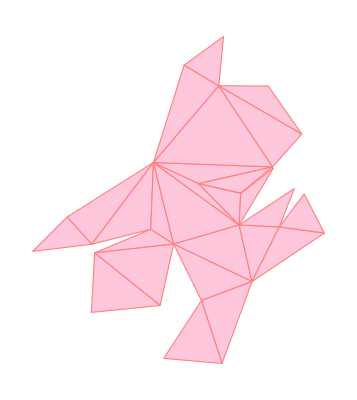
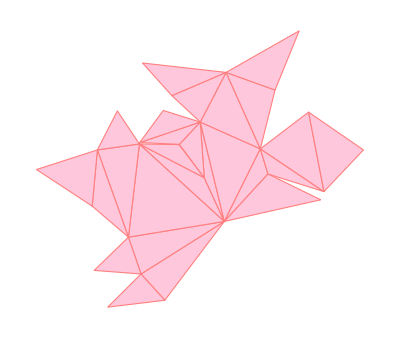
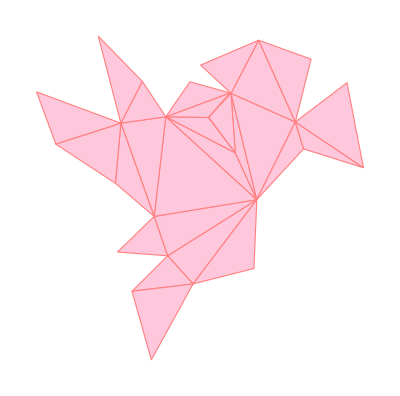
-Graphics3D-{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
generateallnets[polyhedron]
```

## Conclusion

Overall, the results were satisfactory. The algorithm returned a successful result for every random polyhedron that I tested, although it took quite long for polyhedron with many sides.

## Future work

A possible extension would be to apply a similar algorithm to non convex polyhedra and showing that it is impossible to generate a non overlapping net in some cases. Additional optimization algorithms could also be implemented to speed up the unfolding process.

## Acknowledgements

I would like to sincerely thank my mentor, Jeremy Stratton-Smith, for providing advice and help throughout the entire project process. I would also like to thank Chip Hurst for his unfolding algorithm and tips for 3D transformations. Lastly, I would like to thank the Wolfram Summer Camp team for providing me with this invaluable opportunity.